## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="DDPA";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
pathMASSef = "C:/MASSef/";
kineticDataFileName =  "kinetic_data.csv";

mainFolder = "fit_DDPA_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:C:\MASSef\Enzyme_dummies\DDPA\

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(e4p^c+pep^c⇌(2dda7p)^c+pi^c)^DDPA

Ordered Sequential Bi Bi;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | Null
pep | Null | 1.4×10^12 | 1.33×10^12
1.47×10^12 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | 0.000021 | 0.00001995
0.00002205 |  | M | 6.8 | 25 |  | 
1 | pep | 5.×10^-6 | 4.75×10^-6
5.25×10^-6 | D-arabinose5-phosphate | Null | M | 7.5 | 25 |  | 
1 | pep | 5.3×10^-6 | 5.035×10^-6
5.565×10^-6 | erythrose4-phosphate | Null | M | 7.5 | 25 |  | 
1 | pep | 0.00001 | 9.5×10^-6
0.0000105 | ribose5-phosphate | Null | M | 7.5 | 25 |  | 
1 | pep | 0.000015 | 0.00001425
0.00001575 | 2-deoxyribose5-phosphate | Null | M | 7.5 | 25 |  | 
1 | e4p | 0.000141 | 0.00013395
0.00014805 |  | M | 7.5 | 25 |  | 
1 | e4p | 0.0000814 | 0.00007733
0.00008547 |  | M | 7 | 25 |  | 
1 | pep | 0.000013 | 0.00001235
0.00001365 |  | M | 7 | 25 |  | 
1 | e4p | 0.000086 | 0.0000817
0.0000903 |  | M | 6.8 | 25 |  | 
1 | pep | 9.×10^-6 | 8.55×10^-6
9.45×10^-6 |  | M | 6.8 | 25 |  | 
1 | e4p | 0.0000965 | 0.000091675
0.000101325 |  | M | 7 | 37 |  | 
1 | pep | 5.85×10^-6 | 5.5575×10^-6
6.1425×10^-6 |  | M | 7 | 37 |  | 
1 | e4p | 0.00025 | 0.000198
0.000302 |  | M | 6.4 | 25 |  | 
1 | pep | 0.000035 | 0.000031
0.000039 |  | M | 6.4 | 25 |  | 
1 | e4p | 0.0009 | 0.0006
0.0012 |  | M | 7 | 37 |  | 
1 | pep | 0.00008 | 0.00004
0.00012 |  | M | 7 | 37 |  | 
1 | pep | 9.×10^-6 | 8.55×10^-6
9.45×10^-6 |  | M | 7.5 |  |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | Null
pep | Null | 213.2 | 202.54
223.86 | 1/s | 6.8 | 37 |  | 
1 | e4p | Null
pep | Null | 88.5829 | 84.1538
93.0121 | 1/s | 7 | 37 |  | 
1 | e4p | Null
pep | Null | 96.09 | 91.2855
100.894 | 1/s | 6.8 | 37 |  | 
1 | e4p | Null
pep | Null | 122. | 115.9
128.1 | 1/s | 7 | 37 |  | 
1 | e4p | Null
pep | Null | 187.075 | 185.574
188.577 | 1/s | 6.4 | 37 |  | 
1 | pep | Null | 32 2.5^(0.1 (37-)) | 30.4 2.5^(0.1 (37-))
33.6 2.5^(0.1 (37-)) | 1/s | 7.5 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | 2-phosphoglycerate | 0.00103 | 0.00093
0.00113 |  |  | M | 7 | 37 |  | 
1 | Kic | 2,3-b1sphosphoglycerate | 0.00068 | 0.00062
0.00074 |  |  | M | 7 | 37 |  | 
1 | Kic | 3-methylphosphoenolpyruvate | 0.00132 | 0.00124
0.0014 |  |  | M | 7 | 37 |  | 
1 | Kic | 3-propylphosphoenolpyruvate | 0.00061 | 0.00058
0.00064 |  |  | M | 7 | 37 |  |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kd | pi | 0.00345 | 0.00318
0.00372 |  | M | 7 | 37 |  | 
1 | Kd | 2dda7p | 0.0000248 | 0.000013
0.0000366 |  | M | 7 | 37 |  |

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities ={1};
kmPriorities = {0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0};
s05Priorities = Null;
kcatPriorities = {0,0,0,1,0,0};
inhibitionPriorities={0,0,0,0};
activationPriorities = Null;
otherParamsPriorities = {0,0};

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(e4p^c+pep^c⇌(2dda7p)^c+pi^c)^DDPA

Ordered Sequential Bi Bi;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | Null
pep | Null | 1.4×10^12 | 1.33×10^12
1.47×10^12 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | 0.0000965 | 0.000091675
0.000101325 |  | M | 7 | 37 |  | 
1 | pep | 5.85×10^-6 | 5.5575×10^-6
6.1425×10^-6 |  | M | 7 | 37 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | e4p | Null
pep | Null | 122. | 115.9
128.1 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_DDPA[c] + pep[c] <=> E_DDPA[c]&pep",
				"E_DDPA[c]&pep + e4p[c] <=> E_DDPA[c]&pep&e4p",
				"E_DDPA[c]&pep&e4p <=> E_DDPA[c]&2dda7p&pi",
				"E_DDPA[c]&2dda7p&pi <=> E_DDPA[c]&2dda7p + pi[c]",
                                            "E_DDPA[c]&2dda7p <=> E_DDPA[c]+ 2dda7p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((DDPA^c)_^+pep^c⇌(DDPA^c&pep^c)_^)^DDPA1,((DDPA^c&(2dda7p)^c)_^⇌(DDPA^c)_^+(2dda7p)^c)^DDPA2,((DDPA^c&pep^c)_^+e4p^c⇌(DDPA^c&pep^c&e4p^c)_^)^DDPA3,((DDPA^c&(2dda7p)^c&pi^c)_^⇌(DDPA^c&(2dda7p)^c)_^+pi^c)^DDPA4,((DDPA^c&pep^c&e4p^c)_^⇌(DDPA^c&(2dda7p)^c&pi^c)_^)^DDPA5}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((DDPA^c)_^+pep^c⇌(DDPA^c&pep^c)_^)^DDPA1,Overscript[(DDPA^c&(2dda7p)^c)_^⇌(DDPA^c)_^+(2dda7p)^c, DDPA2],((DDPA^c&pep^c)_^+e4p^c⇌(DDPA^c&pep^c&e4p^c)_^)^DDPA3,Overscript[(DDPA^c&(2dda7p)^c&pi^c)_^⇌(DDPA^c&(2dda7p)^c)_^+pi^c, DDPA4],((DDPA^c&pep^c&e4p^c)_^⇌(DDPA^c&(2dda7p)^c&pi^c)_^)^DDPA5};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((DDPA^c&pep^c&e4p^c)_^-((DDPA^c&(2dda7p)^c&pi^c)_^)/K_DDPA5) Volume_c k_DDPA5^⟶}

Volume_c (-(DDPA^c&(2dda7p)^c&pi^c)_^ k_DDPA5^⟵+(DDPA^c&pep^c&e4p^c)_^ k_DDPA5^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList= {};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	2dda7p[c]	e4p[c]	pep[c]	pi[c]	param_DDPA_total	param_pH	param_Temp	FileFlag	Target_Data

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	0.4405116176334556
1	0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.1368068886032101
1	0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310197
1	0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.2847472489508014
1	0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.38686317984685703
1	0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000001
1	0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491988
1	0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909091
1	0	0.0001345263278918314	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.09090909090909088
1	0	0.0002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.13680688860321
1	0	0.00033791485771230003	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.20076000891310167
1	0	0.0005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508014
1	0	0.0008488037460930167	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468568
1	0	0.0013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.49999999999999994
1	0	0.002132098612825553	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.613136820153143
1	0	0.0033791485771230037	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491987
1	0	0.005355589576196904	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868981
1	0	0.008488037460930166	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.8631931113967899
1	0	0.013452632789183142	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.909090909090909
1	0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.0909090909090909
1	0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321005
1	0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310167
1	0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508014
1	0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468568
1	0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491987
1	0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.86319311139679
1	0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909091
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1061.8335192343566
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2250259996863124e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating other data...

Simulating custom ratios data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/haldaneRatio_1.txt"	100.
1	0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.09090909090909095
1	0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.13680688860321014
1	0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.20076000891310194
1	0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.28474724895080133
1	0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.386863179846857
1	0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.5000000000000002
1	0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.6131368201531432
1	0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7152527510491989
1	0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.7992399910868984
1	0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.86319311139679
1	0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_nad.txt"	0.9090909090909093
1	0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.090909090909091
1	0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.1368068886032102
1	0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2007600089131019
1	0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.2847472489508017
1	0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.3868631798468571
1	0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.5000000000000003
1	0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.6131368201531434
1	0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7152527510491988
1	0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.7992399910868984
1	0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.86319311139679
1	0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_g3p.txt"	0.9090909090909092
1	0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.09090909090909094
1	0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.13680688860321008
1	0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.20076000891310175
1	0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.2847472489508015
1	0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.3868631798468569
1	0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.5
1	0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.6131368201531432
1	0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7152527510491988
1	0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.7992399910868982
1	0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.8631931113967899
1	0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/relRateFor_pi.txt"	0.9090909090909092
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	1	1	0	1	1	8.9	37	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/absRateFor.txt"	1059.363016156407
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/KdRatio_nad.txt"	3.2e-7
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.
1	0	0	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/fit_GAPD_typeII/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=5;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	5
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\absRateFor.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\absRateRev.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\relRateFor_e4p.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\relRateFor_pep.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\relRateRev_2dda7p.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\relRateRev_pi.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	10
filesWithFunctions	[C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\absRateFor.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\absRateRev.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\relRateFor_e4p.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\relRateFor_pep.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\relRateRev_2dda7p.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\relRateRev_pi.txt, C:\MASSef\Enzyme_dummies\DDPA\fit_DDPA_typeII\input\haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.953059331686
best_fit: 1.09847175162
best_fit: 0.999209875093
best_fit: 1.08977511908
best_fit: 1.08677772761

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | haldaneRatio_1 | 1.82379×10^-11 | 3.32619×10^-22 | 58.7888 | 4.1992×10^-9 | 1.4×10^12 | 1.4×10^12
1 | relRateFor_e4p | 0.0000155718 | 2.42481×10^-10 | 3.25952×10^-6 | 0.00358547 | 0.0909091 | 0.0909058
1 | relRateFor_e4p | 0.0000126697 | 1.60521×10^-10 | 3.99101×10^-6 | 0.00291726 | 0.136807 | 0.136803
1 | relRateFor_e4p | 8.62591×10^-6 | 7.44063×10^-11 | 3.98743×10^-6 | 0.00198617 | 0.20076 | 0.200756
1 | relRateFor_e4p | 3.31531×10^-6 | 1.09913×10^-11 | 2.17369×10^-6 | 0.000763375 | 0.284747 | 0.284745
1 | relRateFor_e4p | 3.14168×10^-6 | 9.87013×10^-12 | 2.79857×10^-6 | 0.0007234 | 0.386863 | 0.386866
1 | relRateFor_e4p | 0.0000102956 | 1.06×10^-10 | 0.0000118534 | 0.00237069 | 0.5 | 0.500012
1 | relRateFor_e4p | 0.0000174497 | 3.04493×10^-10 | 0.000024636 | 0.00401803 | 0.613137 | 0.613161
1 | relRateFor_e4p | 0.000023907 | 5.71546×10^-10 | 0.0000393743 | 0.00550495 | 0.715253 | 0.715292
1 | relRateFor_e4p | 0.000029218 | 8.53693×10^-10 | 0.0000537723 | 0.00672792 | 0.79924 | 0.799294
1 | relRateFor_e4p | 0.0000332622 | 1.10637×10^-9 | 0.0000661136 | 0.0076592 | 0.863193 | 0.863259
1 | relRateFor_e4p | 0.0000361646 | 1.30788×10^-9 | 0.0000757051 | 0.00832756 | 0.909091 | 0.909167
1 | relRateFor_pep | 9.43329×10^-7 | 8.89869×10^-13 | 1.97463×10^-7 | 0.000217209 | 0.0909091 | 0.0909089
1 | relRateFor_pep | 7.67432×10^-7 | 5.88953×10^-13 | 2.41748×10^-7 | 0.000176708 | 0.136807 | 0.136807
1 | relRateFor_pep | 5.22342×10^-7 | 2.72841×10^-13 | 2.41461×10^-7 | 0.000120274 | 0.20076 | 0.20076
1 | relRateFor_pep | 2.00473×10^-7 | 4.01894×10^-14 | 1.31441×10^-7 | 0.0000461606 | 0.284747 | 0.284747
1 | relRateFor_pep | 1.90872×10^-7 | 3.6432×10^-14 | 1.70026×10^-7 | 0.0000439498 | 0.386863 | 0.386863
1 | relRateFor_pep | 6.24453×10^-7 | 3.89941×10^-13 | 7.18928×10^-7 | 0.000143786 | 0.5 | 0.500001
1 | relRateFor_pep | 1.05803×10^-6 | 1.11944×10^-12 | 1.49373×10^-6 | 0.000243622 | 0.613137 | 0.613138
1 | relRateFor_pep | 1.44938×10^-6 | 2.1007×10^-12 | 2.38703×10^-6 | 0.000333733 | 0.715253 | 0.715255
1 | relRateFor_pep | 1.77125×10^-6 | 3.13733×10^-12 | 3.25967×10^-6 | 0.000407846 | 0.79924 | 0.799243
1 | relRateFor_pep | 2.01634×10^-6 | 4.06564×10^-12 | 4.00764×10^-6 | 0.000464281 | 0.863193 | 0.863197
1 | relRateFor_pep | 2.19224×10^-6 | 4.80592×10^-12 | 4.58894×10^-6 | 0.000504783 | 0.909091 | 0.909095
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.
1 | absRateFor | 8.33245×10^-12 | 6.94297×10^-23 | 2.3408×10^-9 | 1.91869×10^-9 | 122. | 122.

### Simulated Data and Best Fit Data Plot

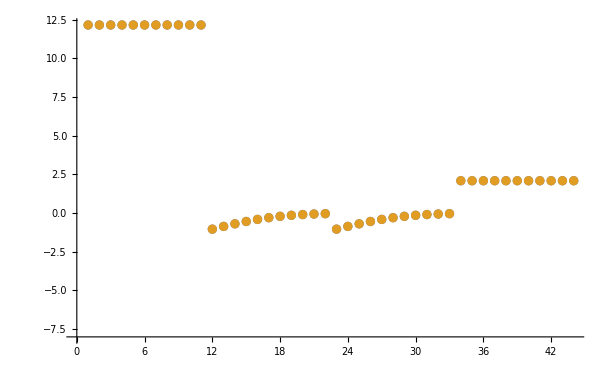

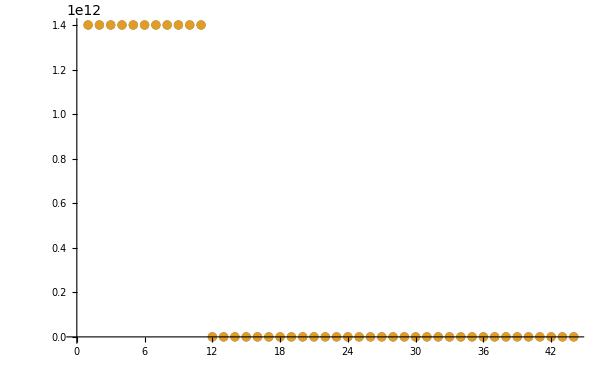

```mathematica
dataSetI=5;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

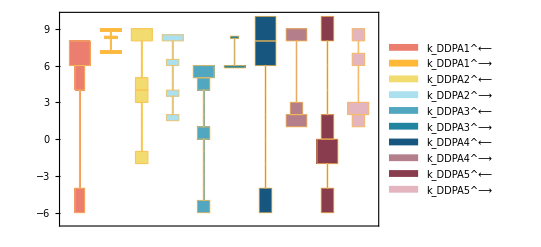

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

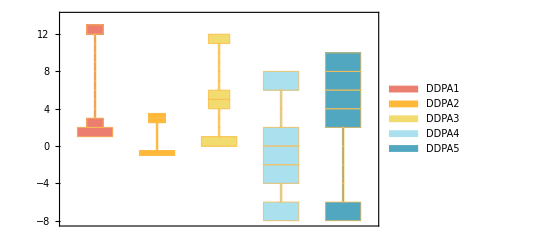

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

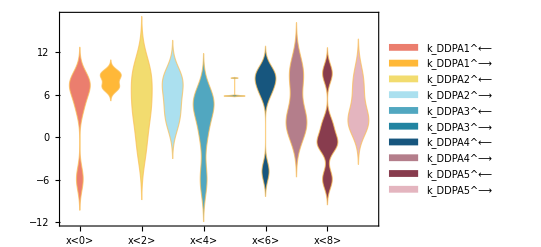

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

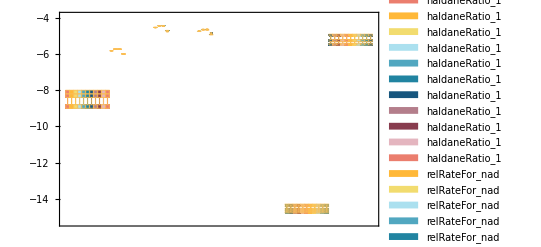

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

data value | predicted value | error in %
0.000045 | 0.000044999 | 0.00221261
0.00089 | 0.00088961 | 0.0437745
0.00053 | 0.000529862 | 0.0260555

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
1059.36 | 1059.36 | 0.0000114381

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 2.37024×10^-7

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

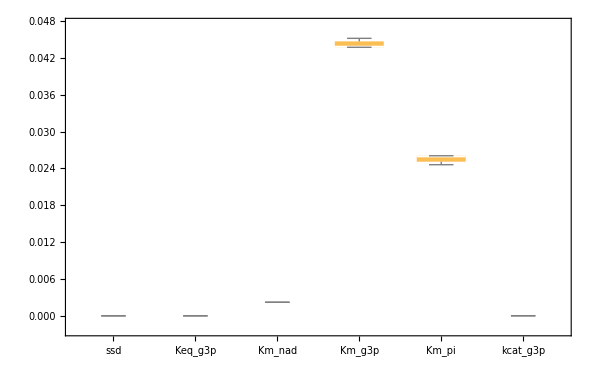

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```